```mathematica
(* Present goal: to calculate the transmission for N-th mode of the transverse momentum, starting from the t[ϕ_,el_,dl_]


****Updated notes:

August 31st - I now realize that Equation 12 in DeMartino, restricts very severaly the parameters we can have for our devices. To see this, you can let epsilon in Equation 12 to be equal to the kF (Fermi wavenumber) in our device (due to the difference in units). For realistic device , we usally have kF of the order 10^8 m^-1. WE can do smallet in the 10^7 regime, but not much bigger. Now if you let d = 100 nm, the you find that lb must be smaller than 32nm - if bigger all electrons are reflected (cannot calculate phi). This means a maximum B field of only 0.6 Tesla or so = very low, and outside the QH regime.

What to do:

(A) we do not need to focus on the QH regime for now (DeMartino is not even the full model - I believe that the condition in Equation 2 could change later when we put a magnetic field in the contacts)
For now, let takes the most optimistic numbers and focus on exploring what is possible with DeMartino.
This means maximizing the energy in the contacts + channel (largest possible gate capacitance and channel doping), and reducing the length of the channel to a minimum.

(B) later we can see if for the Zubarev case more scenarios are possible.



Steps: (i) define all experimental parameters
(ii) calculate the physical quantities from parameters: energy, momenta, phi
(iii)calculate Tn for a specific set of experimental values
(iv) generalize the procedure to create a function Tn which works for any set of parameters automatically

(i) First we define the dimensions of the device we wish to study. For such a study, and based on our experimental capabilities, we choose:
(again trying to maximize the interesting physics but satisfiying Equation 12)

L= 80 nm (means that d = +-40nm), W =1000 nm, S= Area = 1*10^(-13)m^2
Lsus (suspension length inclusing both the channel and contacts) = 2000 nm; 
   Height of suspension = dair = 50 nm;   
    dsio2 = 0 nm (we assume all oxide was etched)
Capacitance = cBG=(ϵair *ϵsio2)/((dsio2*ϵair)+(dair*ϵsio2)) ; 
	cBG=(ϵair )/(dair) = 1.77*10^(-4) F/m^2

The we set the magnetic field (B) and gate values (Vg) to achieve some desired Landau level filling fraction (nu or ν). To keep things simple we will use the simplest ones in graphene:
ν= 18 
(taking a large ones helps with condition of Eq. 12)
  also use 17.5(metallic phase - not a quantum Hall state)  
(note that -ve fractions means that either we reverse the direction of the magnetic field OR we change the sign of the charge carriers from electrons to holes) 

remember that nu = (density of charge carriers per unit area (nc))/ (density of quanta of magnetic flux per unit area (nf)); one quantum of flux = h/e = Subscript[ϕ, o]

To calculate these 2 quantities 
nc = cBG * (Vg-Vd))/ e(note cBG is already per units area)
   nf = (B*S) / ((h/e) *S)
we use the largest possible Vg to increase EF, and increase the B range satisfying Equation 12.
for example, we use Vg-Vd = 5 volt, for simplicity, we set the Dirac point voltage Vd = 0

Vg* (cBG/e)= 5*1.77*10^(-4)/e = 8.85*10^15 m^-2 

Thus, to achieve ν=18, we need 18 electrons for each Subscript[ϕ, o]  
So we need nf = (8.85*10^15 m^-2) / 18  = 4.91*10^14 m^-2

 area of one flux = (h/e)/ B(in Tesla)= 4.14*10^-15 / B 
number of flux per square meter =1/(area of one flux)
= B/ 4.14*10^-15 m^-2  = 4.91*10^14 m^-2
gives  B = 2.03 Tesla


so to achieve ν=18 in our device we simply need to set
B = 2.03T Tesla, and Vg = 5.0 V

Now, checking if this is possible using Equation 12,


(ii) calculating the physical quantities

The Fermi energy in the contact,μCont is set by material parameters:
a realistic one we can use is μCont= between 50 meV and 100 meV, maybe up to 150 meV 

The Fermi energy in the channel, μCH, is determined by the Vg-Vd values we are applying AND by the nimp (number of charge carriers from impurities). For simplicity, we can make the reasonable approximation that our Vg is big enough and our sample clean enough that we can neglect nimp, so we set nimp =0.
Then, μCH = hbar*vF*√(π*Abs[nc])
nc=cBG/e*(Vgate-Vdirac)  (when there is no strain)
so for ν=18, Vg-Vd = 5.0 V, nc=2.2*10^16 m^-2
μCH = 0.087eV, kF = 1.32*10^8 m^-1

***Checking if our numbers are allowed by Equation 12
max lb from Equation 12 for d = 40 nm, E = 1.32*10^8 m^-1 is 
lb > 17.3 nm , so Bmax = 2.20 Tesla !! IT works! but it was not easy.

In summary: for ν=18, μCont or/and μCH = 87 meV 
(we can study the case when both are at ν=18 to start, then later, contact and channel can have different ν - actually, for now, there is no B in the contact so there is no Landau level there, but I just mean that the charge density is the same)


Now that we know the energy, we need to get the momenta values,
ky = quantized due to the width of the flake. We start in the contacts, where B=0, A=0, thus ky (called qn in the code) q[N_,W_]:=π/W*(N+1/2)
for W= 1000nm, and ν=2, μCont= 87 meV, what are the possible values of qn in the contacts ?
what is kF_contact = (μCont/hbar*vF) = 1.32*10^8 m^-1
π/W = 3.14 *10^6
Nmax =  (kF_contact / (π/W)) - 1/2 = 42.0 -0.5 = 41.5
this measn that N=0, 1,2,3,... 41 are allowed , but N=42 is forbidden
 (energy would not be conserved because hbar*vF*qn > μCont)
So there are actually 42 mode (0 to 41) allowed for +ve N's (angles bigger than zero), but remember that qn can also be negative, so there are also 42 modes (0 to -41) for negative angles between 0 and -90 degree. Double counting the zero is RIGHT, because the zero mode is split into two, N = 0 + 1/2, OR N= 0 -1/2, then N = -1-1/2, -2-1/2 ... (for the negative modes)
and N= 0+1/2, 1+1/2, 2+1/2, for the positive mode.

Now we can calculate Phi, ϕ , which corresponds to each mode N!!

(ϕ = incident angle, the one which enters the transmission formula, note that ϕ1 can be calculated from ϕ, so if we know ϕ, we know ϕ1)

at the source contact-channel interface
A = -d*c/(e(lb^2)), after calcelling the terms, this just give A = -d*B
in our device we use L instead of d, so -d, means -L/2
--later on: we will need to think if we want to keep this coordinate systems, from -L/2 to +L/2, basically L =2d. OR go back to the original coordinates from Linxiang from 0 to L. **The Linxiang transmission equation is currently written for 0 to L**

ok, so at the contact-channel edge, we have Ay = -L/2*B (wrong units!!), 
the units in DeMartino are not the same as for us! first they set hbar=1, and use CGS units
For us:
**lb = Sqrt[hbar/(e*B)] in SI  units ***
for example at B=2.03 T
we get lb = 18 nm 

***In our Units, (basically replace their c with hbar), we have
lb = Sqrt[hbar/(e*B)] ; remember B = 2.03 T ( gives lb =10.5 nm)
A(-d)= -d*hbar / (e*lb^2) = -d*B, where d= L/2 = 40 nm
B has units of Tesla = V.s/m^2
we get A(-d) = -d*B= -8.12*10^-8 (V.s/m)
to compared with the A from strain (different units)
A_from_B = (hbar/e) * A_strain = 6.6*10^-16*A_strain

A_from_B = 8.12*10^-8 (V.s/m) corresponds to A_strain = 1.23*10^8 m^-1 

could include both in the Hamiltonian by writing 
A_total = A_strain - (e/(hbar))*A_from_B
and then use the same Hamiltonian as Linxiang,  
     but replace his A by A_total

**note for A_from_B, A only has a Ay component, Ax=0.


and this is what we use to calculate ϕ
so qn= π/W*(N+1/2) - Ay_total  
here Ay_total (at -d=-L/2) = 1.23*10^8 m^-1 
 ϕ = ArcSin(qn/kF_contact)
So for example for modes N =0,1,...  ; 
q0 = 1.57*10^6 - 1.23*10^8 m^-1 = -1.214*10^8 m^-1; q1 = 4.71*10^6 - 1.23*10^8 m^-1 = -1.183*10^8 m^-1, ..
for ν=18, μCont= μCH = 87 meV, kF_CH= 1.32*10^8 m^-1

we get Subscript[ϕ, N0],Subscript[ϕ, N1],Subscript[ϕ, N2],Subscript[ϕ, N3] = ArcSin(qn/kF_contact)
Subscript[ϕ, N0] = -1.16787,Subscript[ϕ, N1] =-1.11094, = ... 
(for the positive N's, the negative N's have negative angles, BUT now the Ay (from B) does not change sign for the negative mode, so the angles will NOT be exactly the same for negative modes)

(iv) There are only 82 modes - so please
Do manually (for loop) all modes for the above parameters, 
and calculate the transmission Tn for all modes
then calculate G = ... for this situation (

***next: check if the values of "dl" and "el" are the same for our units and for DeMartino's units

I have not checked this carefully, but I think that yes, the lb and el values are the same for us and DeMartino since these quantities are unitless

***Then, see how you can made this calculation of what is the angle for each mode N automatic -- i.e. write an expression for Subscript[ϕ, N] , and all other parameters which enter your t[ϕ_,el_,dl_]

and then check that this automated calculation gives all of the same values as the ones you calculated manually

once that is does, you can use this script to calculate G at all Vg-Vd (just a for loop - using the Linxiang code). And create G-Vg plots in Igor.

For now always do the same Fermi energy in the Source and Channel, and we can try other situations later. 



*)
```

```mathematica
ClearAll["Global`*"]
(*momenta parameters*)
ϕ1[ϕ_,el_,dl_]:=ArcSin[2*(dl)*(1/(el))+Sin[ϕ]]
(*py[ϕ_]:=ϵ*Sin[ϕ]+(d/(lb)^2)*)
px[ϕ_]:=Cos[ϕ]
px1[ϕ_,el_,dl_]:=Cos[ArcSin[2*(dl)*(1/(el))+Sin[ϕ]]]
(*Operators u*)
u1p[ϕ_,el_,dl_]:=ParabolicCylinderD[(((el)^2)/2)-1,Sqrt[2]*((-dl)+el*Sin[ϕ]+dl)] 
u1m[ϕ_,el_,dl_]:=ParabolicCylinderD[(((el)^2)/2)-1,-1*Sqrt[2]*((-dl)+el*Sin[ϕ]+dl)]
u2p[ϕ_,el_,dl_]:=ParabolicCylinderD[(((el)^2)/2)-1,Sqrt[2]*((dl)+el*Sin[ϕ]+dl)]
u2m[ϕ_,el_,dl_]:=ParabolicCylinderD[(((el)^2)/2)-1,-1*Sqrt[2]*((dl)+el*Sin[ϕ]+dl)]
(*Operators v*)
v1p[ϕ_,el_,dl_]:=ParabolicCylinderD[((el)^2)/2,Sqrt[2]*((-dl)+el*Sin[ϕ]+dl)]
v1m[ϕ_,el_,dl_]:=ParabolicCylinderD[((el)^2)/2,-1*Sqrt[2]*((-dl)+el*Sin[ϕ]+dl)]
v2p[ϕ_,el_,dl_]:=ParabolicCylinderD[((el)^2)/2,Sqrt[2]*((dl)+el*Sin[ϕ]+dl)]
v2m[ϕ_,el_,dl_]:=ParabolicCylinderD[((el)^2)/2,-1*Sqrt[2]*((dl)+el*Sin[ϕ]+dl)]
(*T[ϕ_]:=(8*((3.7)^4)*Cos[ϕ1[ϕ]]*Cos[ϕ]*((u2p[ϕ]*v2m[ϕ]+v2p[ϕ]*u2m[ϕ])^2))*)
(*D operator*)
Dop[ϕ_,el_,dl_]:=((el)^2)*Exp[I*(ϕ1[ϕ,el,dl]-ϕ)]*(u1p[ϕ,el,dl]*u2m[ϕ,el,dl]-u2p[ϕ,el,dl]*u1m[ϕ,el,dl])-2*(v1p[ϕ,el,dl]*v2m[ϕ,el,dl]-v2p[ϕ,el,dl]*v1m[ϕ,el,dl])+I*Sqrt[2]*el*(Exp[I*ϕ1[ϕ,el,dl]]*(v1p[ϕ,el,dl]*u2m[ϕ,el,dl]+u2p[ϕ,el,dl]*v1m[ϕ,el,dl])+Exp[-I*ϕ]*(u1p[ϕ,el,dl]*v2m[ϕ,el,dl]+v2p[ϕ,el,dl]*u1m[ϕ,el,dl]))
(*transmission amplitude*)
t[ϕ_,el_,dl_]:=(2*I*el*(u2p[ϕ,el,dl]*v2m[ϕ,el,dl]+v2p[ϕ,el,dl]*u2m[ϕ,el,dl]))/(Exp[I*(px[ϕ]+px1[ϕ,el,dl])*el*dl]*Dop[ϕ,el,dl])

(*Sqrt[2*px1[ϕ,el,dl]/px[ϕ]]*Cos[ϕ]*)
(*(2*I*3.7*Sqrt[2*px1[Pi/2,3.7,0.5]/px[Pi/2]]*Cos[Pi/2]*(u2p[Pi/2,3.7,0.5]*v2m[Pi/2,3.7,0.5]+v2p[Pi/2,3.7,0.5]*u2m[Pi/2,3.7,0.5]))
(Exp[I*(px[Pi/2]+px1[Pi/2,3.7,0.5])*3.7*0.5]*Dop[Pi/2,3.7,0.5])
Sqrt[2*px1[Pi/2,3.7,0.5]/px[Pi/2]]*)
(*px1[Pi/2,3.7,0.5]
px[Pi/2]*)
(*transmission equation*)
T[ϕ_,el_,dl_]:=2*px1[ϕ,el,dl]*Cos[ϕ]*t[ϕ,el,dl]*(t[ϕ,el,dl])*
(* Clear all stored variables, but not functions *)
Clear@@Select[Names["Global`*"],ToExpression[#,StandardForm,Function[sym,OwnValues[sym]=!={},HoldAll]]&]  
(* Boudary condition in graphene for smooth edges (Tworzydolo) *)
q[N_,W_]:=π/W*Sign[N]*(Abs[N]+1/2)

(*Tn[μCont_,μCH_,Nq_,L_,W_,Ay_]:=Tϕ[μCont/(ℏ*vF),μCH/(ℏ*vF),q[Nq,W],L,Ay];*)
(* Export general graphene transmission expression *)
SetDirectory[NotebookDirectory[]];

Export["Tphi_expr_V0.0.mx",T[ϕ,el,dl]]
```

Tphi_expr_V0.0.mx

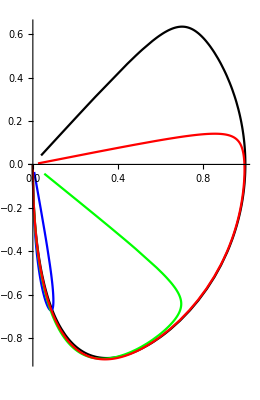

```mathematica
PolarPlot[{T[ϕ,3.7,0.5],T[ϕ,3.7,3.67],T[ϕ,3.7,3],T[ϕ,3.7,1.5]},{ϕ,-Pi/2,Pi/2}, PlotStyle->{Black,Blue,Green,Red}]
```

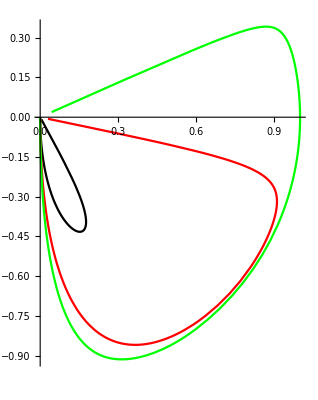

```mathematica
PolarPlot[{T[ϕ,1.6,1.5],T[ϕ,2.5,1.5],T[ϕ,5,1.5]},{ϕ,-Pi/2,Pi/2}, PlotStyle->{Black,Red,Green}]
```

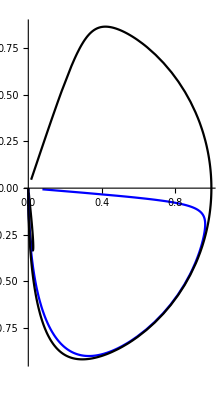

```mathematica
PolarPlot[{T[ϕ,3.7,3.69],T[ϕ,3.7,2.0],T[ϕ,3.7,0.1]},{ϕ,-Pi/2,Pi/2}, PlotStyle->{Black,Blue}]
```